# 2. vaja: Uporaba Mathematice

1. Izračunaj vrednost izraza (x^5−2x^2+3x+4)/(x^5−2x−1) pri x = 1, 2, 3, 4, tako da:
(a) uporabiš ustrezna prepisovalna pravila in ukaz ReplaceAll (oz /.).
(b) definiraš funkcijo in jo pokličeš na več vrednostih

```mathematica
(x^5−2x^2+3x+4)/(x^5−2x−1)/.x->1
```

-3

```mathematica
(x^5−2x^2+3x+4)/(x^5−2x−1)/.x->2
```

34/27

```mathematica
(x^5−2x^2+3x+4)/(x^5−2x−1)/.x->3
```

119/118

```mathematica
(x^5−2x^2+3x+4)/(x^5−2x−1)/.x->4
```

144/145

```mathematica
f[x_]=(x^5−2x^2+3x+4)/(x^5−2x−1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
f[1]
```

-3

```mathematica
f[2]
```

34/27

```mathematica
f[3]
```

119/118

```mathematica
f[4]
```

144/145

```mathematica
Table[f[x],{x,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

2. Deﬁniraj seznam sez z elementi 10,20,30,40,50,60,70. Iz seznama sez tvori nove sezname, ki vsebujejo:
(a) prve tri elemete, 
(b) zadnja dva elementa,
(c) od vključno drugega do četrtega elementa,
(d) natanko drugi, tretji in peti element, 
(e) vse elemente razen četrtega in petega.

```mathematica
seznam=Range[10,70,10]
```

{10,20,30,40,50,60,70}

```mathematica
Take[seznam,3]
```

{10,20,30}

```mathematica
Take[seznam,-2]
```

{60,70}

```mathematica
seznam[[2;;4]]
```

{20,30,40}

```mathematica
seznam[[{2,3,5}]]
```

{20,30,50}

```mathematica
Drop[seznam,{4,5}]
```

{10,20,30,60,70}

3. V seznamu sez z elementi x6,x2,a zamenjaj:
(a) x s 3, 
(b) x z x2, 
(c) x2 z x, 
(d) x z {1,2,3}, 
(e) x z 3, a z x, 
(f) x z 3, a z x in to ponavljaj dokler ni več nobenih x in a (poglej si funkcija ReplaceRepeated).
Tvori nov seznam seznamov, katerega elementi so seznami sez v katerih zaporedoma zamenjamo x z 1,2 in s 3.

```mathematica
sez={x^6,x^2,a}
```

{x^6,x^2,a}

```mathematica
sez/.x->3
```

{729,9,a}

```mathematica
sez/.x->x^2
```

{x^12,x^4,a}

```mathematica
sez/.x^2->x
```

{x^6,x,a}

```mathematica
sez/.x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez/.{x->3,a->x}
```

{729,9,x}

```mathematica
sez//.{x->3,a->x}
```

{729,9,3}

```mathematica
seznam=sez/.x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

4. Izračunaj odvode funkcij simbolično ter v navedenih točkah. 
(a) f(x)= x^5 +4x^3−9, pri x =1 in x =5, 
(b) f(x)= e^4rt(x) x =1 in x =2, 
(c) f(x)=|x+1| (poskusi s FullSimplify, kjer domeno omejiš na realna števila različna od 0), pri x =1, x =−1, 
(d) f(x)= ax^2 +3b, kjer sta a in b neki neznani vredosti, pri x =1 in x =2.

```mathematica
f[x_]=x^5+4x^3−9
```

-9+4 x^3+x^5

```mathematica
D[f[x],x]
```

12 x^2+5 x^4

```mathematica
D[f[x],x] /. x -> 1
```

17

```mathematica
D[f[x],x] /. x -> 5
```

3425

```mathematica
g[x_]=Exp[Surd[x,4]]
```

ⅇ^(x^(1/4))

```mathematica
D[g[x],x]
```

(ⅇ^(x^(1/4)))/(4 (x^(1/4))^3)

```mathematica
D[g[x],x] /. x -> 1
```

ⅇ/4

```mathematica
D[g[x],x] /. x -> 2
```

(ⅇ^(2^(1/4)))/(4 2^(3/4))

```mathematica
h[x_]=Abs[x+1]
```

Abs[1+x]

```mathematica
odvod= FullSimplify[D[h[x],x],x≠0&&Element[x,Reals]]
```

Sign[1+x]

```mathematica
odvod /. x -> 1
```

1

```mathematica
odvod /.x -> -1
```

0

```mathematica
i[x_]=a*x^2+3*b
```

3 b+a x^2

```mathematica
D[i[x],x]
```

2 a x

```mathematica
D[i[x],x] /. x -> 1
```

2 a

```mathematica
D[i[x],x] /. x -> 2
```

4 a

5. Dana je funkcija f(x)= x^3*ln(4x+5).
(a) Zapiši deﬁnicijo funkcije v obliki f[x_] := ... 
(b) Nariši funkcijo na intervalu x ∈[1,10]. 
(c) Za dan x0 =5 izračunaj vrednost funkcije v tej točki.
(d) Izračunaj vrednost smernega koeﬁcienta k0 tangente na graf funkcij v točki x0. 
(e) Izračunaj še odmik n0 tangente t[x]= k0∗x+n0 na graf funkcije, v točki x0. Tangento deﬁniraj kot funkcijo t[x_] = ... 
(f) Nariši na istem grafu hkrati funkcijo f(x) in njeno tangento.
(g) S pomočjo kode napisane v prejšnjih točkah sestavi funkcijo narisi[f_, x0_, interval_], ki nariše graf funkcije f in tangente v točki x0. Npr. klic narisi[f[x], 5, x, 0, 10] nariše natanko isti graf kot prejšnja točka. Preizkusi funkcijo narisi[...] še na dveh drugih funkcijah, ki se jih izmisliš in jih sam deﬁniraš.

```mathematica
f[x_]:=x^3*Log[4x+5]
```

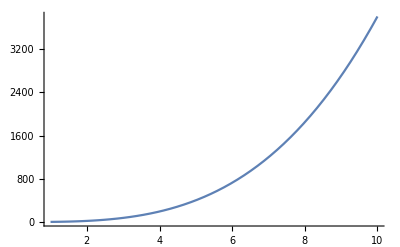

```mathematica
Plot[f[x],{x,1,10},PlotRange->All]
```

```mathematica
f[5]
```

125 Log[25]

```mathematica
x0 =5
```

5

```mathematica
k0 = D[f[x],x] /. x -> 5
```

20+75 Log[25]

```mathematica
y = k0*x + n /.{x ->x0,y-> f[x0]}
```

n+5 (20+75 Log[25])

```mathematica
enacba = f[x0]==k0 *x0+n
```

125 Log[25]==n+5 (20+75 Log[25])

```mathematica
resitev = Solve[enacba,n]
```

{{n→-50 (2+5 Log[25])}}

```mathematica
n0 = n /.resitev //First
```

-50 (2+5 Log[25])

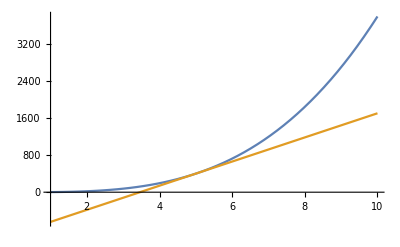

```mathematica
Plot[{f[x],k0*x+n0},{x,1,10}]
```

```mathematica
narisi[f_,x0_,x_,zac_,kon_] := Module[{k0,n,enacba,resitev,n0},
k0 = D[f[x],x] /. x -> x0;
enacba = f[x0] == k0 * x0 +n;
resitev = Solve[enacba,n];
n0 = n/.resitev //First;
Plot[{f[x],k0*x+n0},{x,zac,kon}]]
```

```mathematica
narisi[f,x0,x,1,10]
```

-Graphics-

6. Poračunaj limite:
(a) limx→2 (x^3−4x^2+2x+4 x^5−9x−14)
(b) limx→0 (arctan(7x) arcsin(8x))
(c) limx→5((x2−25)cot(πx)) 
(d) limx→π (1+cosx 2√πx−π−x) 
(e) limx→0+ (|x|cotx) 
(f) limx→0−(|x|cotx)

```mathematica
Limit[(x^3-4*x^2+2*x+4)/(x^5-9*x-14),x->2]
```

-2/71

```mathematica
Limit[(ArcTan[7x])/(ArcSin[8x]),x->0]
```

7/8

```mathematica
Limit[(x^2-25)*Cot[Pi*x],x->5]
```

10/π

```mathematica
Limit[(1+Cos[x])/(2*Sqrt[Pi*x]-Pi-x),x->Pi]
```

-2 π

```mathematica
Limit[Abs[x]*Cot[x],x->0,Direction->1]
```

-1

```mathematica
Limit[Abs[x]*Cot[x],x->0,Direction->-1]
```

1

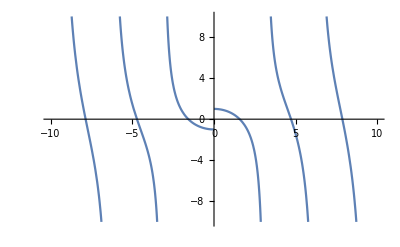

```mathematica
Plot[Abs[x]*Cot[x],{x,-10,10},PlotRange->{-10,10}]
```

7. Nariši graf funkcije y =(x^2−1)/(x^2−4) . Računsko pa pri tem določi (in se potem s sliko prepričaj) naslednje:
(a) ničle funkcije
(b) pole funkcije in obnašanje funkcije v okolicah polov
(c) asimptote
(d) ekstreme
(e) prevoje
(f) intervale konveksnosti in konkavnosti

```mathematica
f[x_] := (x^2−1)/(x^2−4)
```

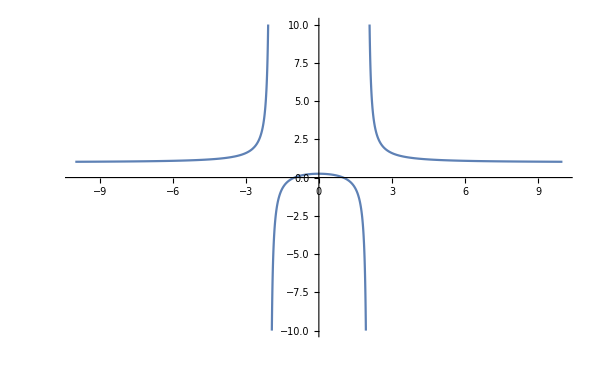

```mathematica
Plot[f[x],{x,-10,10},PlotRange->{-10,10}]
```

```mathematica
Solve[f[x]== 0,x]
```

{{x→-1},{x→1}}

Funkcija ima ničle v -1 in 1.

```mathematica
Solve[1/f[x]== 0,x]
```

{{x→-2},{x→2}}

Funkcija ima pole v -2 in 2.

```mathematica
Limit[f[x],x -> -2,Direction->1]
```

∞

```mathematica
Limit[f[x],x -> -2,Direction->-1]
```

-∞

```mathematica
Limit[f[x],x -> 2,Direction->1]
```

-∞

```mathematica
Limit[f[x],x -> 2,Direction->-1]
```

∞

```mathematica
Limit[f[x],x ->Infinity]
```

1

Enačba asimptote funkcije je y = 1.

```mathematica
Solve[D[f[x],x] == 0,x]
```

{{x→0}}

Funkcija ima maksimum v stacionarni točki 0.

```mathematica
Solve[D[f[x],{x,2}] == 0,x]
```

{{x→-(2 ⅈ)/(√3)},{x→(2 ⅈ)/(√3)}}

Prevoji so kompleksni zato jih ne štejemo.

Intervali konveksnosti : (-inf, -2) U (2,inf)
Intervali konkavnosti: (-2,2)

8. Reši enačbo x^4 + x^3 − x = 0 pri pogoju x > 0 in in izračunaj vrednost te rešitve na kvadrat, ne da bi prepisoval vrednost v naslednjo vrstico

```mathematica
resitve = x /.Solve[x^4+x^3-x == 0 && x > 0]
resitve^2 //N
```

{Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927}

{0.56984}

9. Določi presečišča krivulj 3x^2 − 5y^2 = 5 in 2x^2 + 3y^2 = 59 ter izračunaj presečni kot.

```mathematica
f = 3x^2−5y^2== 5
g = 2x^2+3y^2== 59
```

3 x^2-5 y^2==5

2 x^2+3 y^2==59

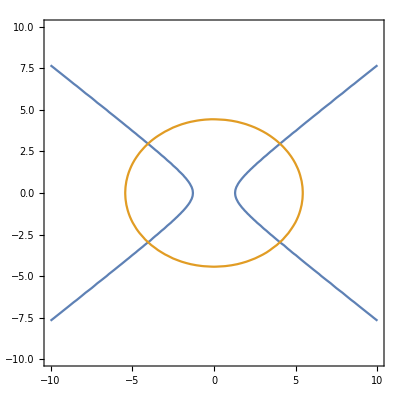

```mathematica
ContourPlot[{3x^2−5y^2== 5,2x^2+3y^2== 59},{x,-10,10},{y,-10,10}]
```

```mathematica
resitev =Solve[f && g && x > 0 && y > 0, {x, y}]
```

{{x→√(310/19),y→√(167/19)}}

```mathematica
x0 = x /. resitev[[1]]
```

√(310/19)

```mathematica
y0 = y /.resitev[[1]]
```

√(167/19)

```mathematica
k1 =D[y/.Solve[enacba1 && x >= 0 && y >= 0, y, Reals]//First, x] /. x-> x0
k2 =D[y/.Solve[enacba2 && x >= 0 && y >= 0, y, Reals]//First, x] /. x-> x0
```

3 √(62/835)

-(2 √(310/167))/3

```mathematica
N[Abs[ArcTan[k1] - ArcTan[k2]]] * 180/Pi
```

81.5141